01010 (-3+2 1)-1/10-20100StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNone,{{x[t],0},x_1},{{f[t],0}},Automatic,t

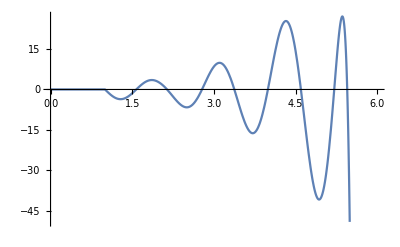

010000001000000100000010-1200-3012-246-556/5-121/101-2400-1200-240-2000StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4$CellContext`stname5Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1151FalseFalseFalseAutomaticNoneAutomatic

```mathematica
lathe=StateSpaceModel[10x''[t]==-100 x[t]-x'[t]-200 (f[t]+x[t]-x[t-1]),{x[t],x'[t]},{f[t]},x[t],t]
OutputResponse[lathe,DiracDelta[t-1],{t,0,5}];
Plot[%, {t,0,6}]
latheApprox=SystemsModelDelayApproximate[lathe,3]
```

```mathematica
openlooppoles=Eigenvalues[Normal[latheApprox][[1]]]
FullSimplify[%] //N
```

{Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832,Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832,Root0.904+5.28 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,5]0.904076946287601,Root0.904-5.28 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,4]0.904076946287601,Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695}

{-6.74923+7.52257 ⅈ,-6.74923-7.52257 ⅈ,0.904077+5.2782 ⅈ,0.904077-5.2782 ⅈ,-0.409685}

```mathematica
l=EstimatorGains[latheApprox,Join[Drop[Sort[openlooppoles],-2],{-4+I,-4-I}]];
(*
A = [0 1 0 0 0; 0 0 1 0 0; 0 0 0 1 0; 0 0 0 0 1; -1200 -3012 -246 -556/5 -12.1];
B = [0;0;0;0;1];
C = [-2400 -1200 -240 -20 0];
D = 0;
lathe_approx = ss(A, B, C, D);
p = [-0.40968528806553695,-6.749234302254832-7.522569313686051i,-6.749234302254832+7.522569313686051i,-4+1i,-4-1i];
L = place(A',C',p)';
K= [-488.6222131578468,-846.8212580038667, 893.6550622979755, 124.73656788522807, 9.808153892575204];
controller = reg(lathe_approx , K, L);

DelayT = struct('delay',1,'a',[0 0;20 0],'b',0,'c',0,'d',0);
lathe = delayss([0,1;-30,-0.1],[0;-20],[1,0],0,DelayT);

controlled_system = feedback(lathe, controller, +1);
impulse(pade(controlled_system, 10));

t = 0:0.01:5;
u = dirac(t - 1);
lsim(lathe, u, t);
impulse(pade(lathe, 5));
*)
```

```mathematica
k=StateFeedbackGains[latheApprox,Join[Drop[Sort[openlooppoles],-2],{-4+I,-4-I}]];
```

```mathematica
controller=EstimatorRegulator[latheApprox,{l,k}];
```

(1200+430 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695+430 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832+80 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832+430 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+80 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+80 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+7 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832)/20001+(1200+430 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695+430 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832+80 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832+430 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+80 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+80 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+7 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832)/4000(1200+430 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695+430 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832+80 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832+430 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+80 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+80 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+7 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832)/20000(1200+430 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695+430 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832+80 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832+430 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+80 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+80 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+7 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832)/2400000(1200+430 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695+430 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832+80 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832+430 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+80 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+80 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+7 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832)/48000001/200 (180-120 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695-120 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832-43 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832-120 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832-43 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832-43 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832-8 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832)1/400 (180-120 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695-120 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832-43 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832-120 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832-43 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832-43 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832-8 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832)1+(180-120 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695-120 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832-43 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832-120 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832-43 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832-43 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832-8 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832)/2000(180-120 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695-120 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832-43 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832-120 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832-43 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832-43 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832-8 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832)/240000(180-120 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695-120 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832-43 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832-120 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832-43 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832-43 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832-8 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832)/4800001/200 (-28200-180 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695-180 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832+120 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832-180 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+120 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+120 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+43 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832)1/400 (-28200-180 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695-180 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832+120 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832-180 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+120 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+120 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+43 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832)(-28200-180 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695-180 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832+120 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832-180 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+120 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+120 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+43 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832)/20001+(-28200-180 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695-180 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832+120 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832-180 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+120 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+120 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+43 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832)/240000(-28200-180 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695-180 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832+120 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832-180 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+120 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+120 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+43 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832)/4800003/10 (6860+470 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695+470 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832+3 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832+470 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+3 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+3 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832-2 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832)3/20 (6860+470 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695+470 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832+3 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832+470 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+3 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+3 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832-2 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832)3/100 (6860+470 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695+470 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832+3 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832+470 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+3 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+3 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832-2 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832)1/400 (6860+470 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695+470 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832+3 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832+470 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+3 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+3 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832-2 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832)1(6860+470 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695+470 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832+3 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832+470 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+3 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+3 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832-2 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832)/800017 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+3/10 (-36644-6860 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695-6860 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832-470 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832-6860 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832-470 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832-470 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832-3 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832)-17 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832-17 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832-17 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+8 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+3/20 (-36644-6860 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695-6860 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832-470 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832-6860 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832-470 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832-470 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832-3 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832)17 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695+17 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832-8 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832+17 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832-8 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832-8 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+3/100 (-36644-6860 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695-6860 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832-470 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832-6860 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832-470 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832-470 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832-3 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832)-17+8 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695+8 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832-Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832+8 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832-Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832-Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+1/400 (-36644-6860 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695-6860 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832-470 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832-6860 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832-470 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832-470 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832-3 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832)-121/10+1/10 (41+10 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695+10 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832+10 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832)(-36644-6860 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695-6860 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832-470 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832-6860 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832-470 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832-470 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832-3 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832)/8000-1200-17 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832-3012+17 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832+17 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+17 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832-8 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832-246-17 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695-17 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832+8 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832-17 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+8 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+8 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832-Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832-471/5-8 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695-8 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832+Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832-8 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832+Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.7492343022548321/10 (-41-10 Root-0.410Root[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,1]-0.40968528806553695-10 Root-6.75-7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,2]-6.749234302254832-10 Root-6.75+7.52 ⅈRoot[12000+30120 #1+2460 #1^2+1112 #1^3+121 #1^4+10 #1^5&,3]-6.749234302254832)0StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4$CellContext`stname5Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1151FalseFalseFalseAutomaticNoneAutomatic
 |  |  |  |

0.1.0.0.0.0.0.0.10. (-3.+2. 1.)-0.1-9772.44+0. ⅈ-16936.4+0. ⅈ17873.1+0. ⅈ2494.73+0. ⅈ196.163+0. ⅈ-20.0.000737558-9.4739×10^-20 ⅈ0.1.77014-2.27374×10^-16 ⅈ1.88507-1.13687×10^-16 ⅈ0.177014-2.27374×10^-17 ⅈ0.0147512-1.89478×10^-18 ⅈ0.0.-0.00509609+0. ⅈ0.-12.2306+0. ⅈ-6.11531+0. ⅈ-0.223061+0. ⅈ-0.101922+0. ⅈ0.0.-0.0303653+0. ⅈ0.-72.8767+0. ⅈ-36.4383+0. ⅈ-7.28767+0. ⅈ0.392694+0. ⅈ0.0.0.0912341+0. ⅈ0.218.962+0. ⅈ109.481+0. ⅈ21.8962+0. ⅈ1.82468+0. ⅈ1.0.1.03574+0. ⅈ0.1774.41+0. ⅈ-922.287+0. ⅈ-891.077+0. ⅈ-215.222+0. ⅈ-21.9082+0. ⅈ0.1.0.0.0.0.0.0.0.StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4$CellContext`stname5$CellContext`stname6$CellContext`stname7Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1171FalseFalseFalseAutomaticNone,{{x[t],0.},x_1,x_2,x_3,x_4,x_5,x_6},{Automatic},Automatic,t

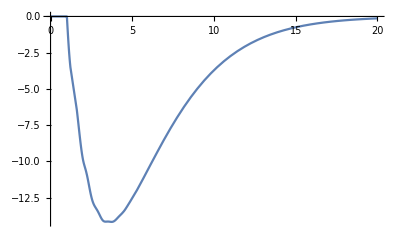

1

```mathematica
closedloopLathe=SystemsModelFeedbackConnect[lathe,controller] // N
OutputResponse[closedloopLathe,DiracDelta[t-1],{t,0,20}];
Plot[%,{t,0,20}]
```